## comment

This notebook produces plots of the orbits generated by local complementation orbit up to and including 8 qubits, where isomorphic are not considered as equal (unless they are equal).

This work refers to “Mapping graph state orbits under local complementation”, https://arxiv.org/abs/1910.03969. Please see this work for associated documentation.

You can choose to import from .mx or .csv. Importing data from .mx is faster, but may not be possible on older versions of Mathematica. Importing from .csv is broken up into qubit number as it can be slow for large number of qubits. Feel free to just import the qubit number you are interested in.

## Load data

#### Constants & Data

Data is organised into nested lists, where the first index, i, gives the qubit number and the second j, indexes the orbit, which are in order as per the canonical listing of Hein, Danielsen, et al. (see references 11, 16 and 17 of the manuscript).

```mathematica
SetDirectory[NotebookDirectory[]];

(* Graph state display options*)
defcol=ColorData[97,"ColorList"][[7]];
graphsize=100;
vertexsize=0.30;
edgethickness =0.024;
impad=10;

(* precompiled import for csv *)
len4={5,11};
len5={6,14,30,132};
len6={7,17,18,38,39,82,40,41,176,372,132};
len7={8,20,22,46,48,48,50,104,106,108,224,50,52,220,110,232,112,236,492,484,1052,504,1056,532,1096,528};
len8={9,23,26,54,27,58,57,61,126,62,130,64,132,134,136,138,284,288,135,139,290,294,612,60,62,63,264,66,138,288,140,140,142,142,296,612,308,300,644,616,145,149,616,302,314,648,306,640,306,656,648,1320,1380,1356,2932,300,312,652,148,636,318,151,318,1368,668,668,660,1408,1404,1380,1428,1424,2952,3004,3024,152,692,680,149,680,1424,1448,1436,1468,3032,3092,3088,2904,660,704,1468,3072,3156,1452,3160,532,3156,1492,1628,3168,3248};
(* Initialise variables *)
lenorbitsLi={{1},{1},{1},len4,len5,len6,len7,len8};
fourLiorbits=Range[2];
fourLigraphlists=Table[0,{i,Range[2]},{j,len4[[i]]}];
four=4;
fiveLiorbits=Range[4];
fiveLigraphlists=Table[0,{i,Range[4]},{j,len5[[i]]}];
five=5;
sixLiorbits=Range[11];
sixLigraphlists=Table[0,{i,Range[11]},{j,len6[[i]]}];
six=6;
sevenLiorbits=Range[26];
sevenLigraphlists=Table[0,{i,Range[26]},{j,len7[[i]]}];
seven=7;
eightLiorbits=Range[101];
eightLigraphlists=Table[0,{i,Range[101]},{j,len8[[i]]}];
eight=8;

(* Minimum graph state chromatic number found each entanglement class *)
χgraph=χorbitsLi;
χgraph[[4]]={2,2};
χgraph[[5]]={2,2,2,3};
χgraph[[6]]={2,2,2,2,2,2,2,3,3,2,3};
χgraph[[6]]={2,2,2,2,2,2,2,3,3,2,3};
χgraph[[7]]={2,2,2,2,2,2,2,2,2,2,2,2,3,3,2,3,3,3,2,3,3,3,3,2,3,3};
χgraph[[8]]={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,2,3,2,2,3,3,3,2,3,2,2,3,3,2,3,2,3,2,3,3,3,2,3,3,3,2,2,3,3,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,2,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3};

(* Minimum graph state chromatic index found each entanglement class *)
χegraph={{1},{2},{2},{3,2},{4,3,2,3},{5,4,3,3,3,2,3,3,3,2,3},{6,5,4,4,3,4,3,3,3,3,2,4,4,4,3,3,3,3,3,3,3,3,3,3,3,4},{7,6,5,5,4,4,5,4,4,4,4,3,3,3,3,3,3,3,4,3,3,3,2,5,4,5,5,4,4,4,4,3,3,4,4,4,3,3,3,3,4,3,4,3,3,3,3,3,3,3,3,3,3,3,2,4,4,3,3,4,3,4,3,4,3,3,3,3,3,3,3,3,3,3,3,4,4,3,4,4,4,4,3,3,3,3,3,3,5,4,3,4,3,4,3,3,3,4,4,5,4}};

(* Graph state rank width of each entanglement class *)
rwdgraphs={{0},{0},{0},{1,1},{1,1,1,2},{1,1,1,1,1,1,1,1,2,2,2},{1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,2,2,2,2,2,2,2,2,2},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,2,2,2,1,2,2,1,1,2,1,2,2,1,2,1,2,2,2,2,2,2,2,2,2,1,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2}};

(* Chromatic number of each orbit *)
χorbitsLi={{1},{1},{2},{2,2},{2,2,3,3},{2,2,2,3,3,3,3,3,3,3,3},{2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3},{2,2,2,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}};

(* Chromatic index of each orbit *)
χeorbitsLi={{1},{1},{3},{4,4},{5,5,5,5},{6,6,5,6,6,6,6,6,6,6,6},{7,7,6,7,7,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,3,7,3,3}};

(* number of edges in each orbit *)
noedgorbitsLi={{1},{1},{1},{12,36},{15,49,130,660},{18,62,67,172,182,436,186,194,1012,2232,792},{21,75,85,214,226,233,243,574,598,622,1416,240,255,1320,626,1448,638,1476,3312,3300,7364,3420,7392,3724,7672,3564},{24,88,103,256,108,280,284,304,712,313,756,323,754,780,794,818,1852,1912,812,828,1928,1980,4480,294,306,316,1628,335,808,1852,830,822,834,834,1912,4272,2036,2004,4648,4356,868,896,4444,2020,2084,4680,2052,4660,2052,4744,4732,10296,10644,10608,23456,1968,2064,4712,896,4476,2112,908,2112,10512,4852,4852,4840,10912,10884,10776,11112,11084,23616,24032,24192,912,5324,4960,904,4960,10952,11192,11168,11392,24256,24736,24704,23232,4620,5104,11392,24576,25248,11352,25280,4256,25248,11632,13024,25344,25984}};

(* number of edges in each orbit *)
noedgorbitsLi={{1},{1},{1},{12,36},{15,49,130,660},{18,62,67,172,182,436,186,194,1012,2232,792},{21,75,85,214,226,233,243,574,598,622,1416,240,255,1320,626,1448,638,1476,3312,3300,7364,3420,7392,3724,7672,3564},{24,88,103,256,108,280,284,304,712,313,756,323,754,780,794,818,1852,1912,812,828,1928,1980,4480,294,306,316,1628,335,808,1852,830,822,834,834,1912,4272,2036,2004,4648,4356,868,896,4444,2020,2084,4680,2052,4660,2052,4744,4732,10296,10644,10608,23456,1968,2064,4712,896,4476,2112,908,2112,10512,4852,4852,4840,10912,10884,10776,11112,11084,23616,24032,24192,912,5324,4960,904,4960,10952,11192,11168,11392,24256,24736,24704,23232,4620,5104,11392,24576,25248,11352,25280,4256,25248,11632,13024,25344,25984}};

(* Smallest number of edges of any graph state found in an orbit *)
minedgeorbitsLi={{1},{2},{1},{3,3},{4,4,4,5},{5,5,5,5,5,5,6,6,6,6,9},{6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,8,8,9,9,10},{7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,12,12,12,13,13,13}};

(* Schmidt measure of each entanglement class. When an exact value is not known, the mean of the upper and lower bounds is given *)
schmidtgraph={{0},{1},{1},{1,2},{1,2,2,2.5},{1,2,2,2,3,3,2,3,3,3,3.5},{1,2,2,2,2,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3.5,3.5,3.5,3.5,3,3.5,3.5},{1,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3.5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3.5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,4,4,4,4,4,4,4,4,4,4,4.5,3.5,4,4,4.5,4.5,4.5,4.5,4,4.5,4.5,4,4.5,4.5}};

(* Diameter of each orbit *)
distsorbitsLi={{1},{1},{1},{2,4},{2,4,5,5},{2,4,4,5,6,6,5,6,6,7,4},{2,4,4,5,5,6,6,6,7,7,7,5,6,6,7,7,7,7,7,7,7,7,7,7,7,7},{2,4,4,5,4,5,6,6,6,6,7,6,6,7,7,7,7,8,8,8,8,8,8,5,5,6,6,6,7,7,7,7,7,7,7,7,8,8,8,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,7,8,8,7,7,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,7,7,8,8,8,8,8,8,8,9,9,9,9,7,8,8,9,9,8,9,6,9,8,8,9,9}};

(* Mean diameter of each orbit *)
meandistsorbitsLi={{1.},{1.},{1.},{1.6,2.109090909090909},{1.6666666666666667,2.241758241758242,2.6344827586206896,3.455933379597502},{1.7142857142857142,2.338235294117647,2.3986928104575163,2.7780938833570414,2.805668016194332,3.242999096657633,2.7884615384615383,2.8353658536585367,3.644935064935065,4.082427614990001,2.8945176960444137},{1.75,2.4105263157894736,2.5108225108225106,2.885024154589372,2.9202127659574466,2.9414893617021276,2.973061224489796,3.4014189693801344,3.4176100628930817,3.4280027691242645,3.8739189622037156,2.9126530612244896,2.9879336349924586,3.7941054379410546,3.4248540450375313,3.8206448723690105,3.4483590733590734,3.84468085106383,4.271372510059113,4.293653645432301,4.722473255599411,4.2907949130613146,4.717212408444636,4.009515313707999,4.7181981801819814,4.273891668104191},{1.7777777777777777,2.466403162055336,2.5938461538461537,2.9664570230607965,2.6324786324786325,3.026618269812462,3.0469924812030076,3.094535519125683,3.5194920634920637,3.124801692226335,3.555635062611807,3.1418650793650795,3.5641915336571826,3.5718774548311076,3.596296296296296,3.5966359885750556,4.0371771263624145,4.047014130855595,3.5868435599778885,3.616619747680117,4.059539434435032,4.072647489029742,4.523223473786678,3.0084745762711864,3.025383395029085,3.1013824884792625,3.908399585205669,3.1463869463869463,3.5690257061250397,3.9618660472319007,3.5729701952723536,3.5940390544707093,3.609129957047248,3.606832484267306,4.000824553366926,4.421573976017029,4.009327805744744,4.057257525083612,4.445891251219535,4.465906451272305,3.631704980842912,3.6308724832214767,4.465104001689368,4.0696574332797955,4.039111943183899,4.459690499360772,4.081324333011893,4.482345461658842,4.088524590163934,4.474674176131074,4.49417539641651,4.947687642153146,4.91017645636935,4.936801314915804,5.371538100271688,3.9672240802675587,4.023868414543656,4.4616305259487525,3.6324692038977755,4.453028277125736,4.0543420034521755,3.6452097130242826,4.053607920163483,4.8929529383077295,4.484554130120569,4.484836922855937,4.506911298110084,4.916723202170964,4.921401636298286,4.942485102626351,4.929595103633605,4.934244395840407,5.364321864160695,5.37077879954045,5.363866004372124,3.640815615196933,4.194222999255498,4.495573074590661,3.6517322691819336,4.4943342285367756,4.8974413132565315,4.909481228069506,4.923409004881931,4.922559710543863,5.3614118488895315,5.365295815627978,5.3669415952909665,5.386323068470063,4.430100703545317,4.472269817664555,4.924292658282394,5.372469608162379,5.369729983790592,4.933588121045047,5.368582030044759,3.5406878778868074,5.372864606243937,4.934586967740311,4.63518421477856,5.369262565662945,5.367322014561376}};

(* Length of the automorphism group of each orbit *)
autlenLiloops={{1},{1},{1},{3,2},{4,3,3,3},{5,4,3,3,3,3,3,3,4,4,5},{6,5,5,4,5,5,4,3,3,4,3,5,4,5,3,4,3,3,3,3,2,4,4,3,3,4},{7,6,6,5,4,5,6,5,4,5,4,6,5,4,4,5,3,4,5,3,3,3,3,6,6,5,6,4,4,4,4,4,4,4,3,4,4,3,3,4,4,3,4,3,4,5,4,3,3,3,2,3,2,3,3,6,4,4,5,4,5,4,3,4,4,2,4,3,2,4,4,2,3,2,4,5,5,5,4,4,5,3,4,3,3,2,3,5,6,5,4,4,3,4,3,5,3,4,4,5,5}};

(* Length of the automorphism group of each orbit, with self-loops removed *)
autlenLinoloops={{1},{1},{1},{3,2},{4,3,2,3},{5,4,3,3,3,2,3,3,4,4,5},{6,5,5,4,4,4,4,3,3,4,2,4,4,5,3,3,3,2,3,3,2,4,4,3,3,5},{7,6,6,5,4,5,5,5,4,5,4,4,3,4,4,4,3,4,5,3,3,3,3,5,5,5,6,4,4,4,5,4,4,4,3,4,3,3,2,5,4,3,4,3,3,5,3,3,3,2,2,3,2,3,3,5,4,3,5,5,4,4,3,4,4,2,4,3,2,3,4,2,3,2,4,6,5,4,4,3,4,4,4,3,3,2,3,5,6,4,4,4,3,5,3,5,3,4,4,5,5}};

(* Is the orbit a tree? *)
treeLi={{True},{True},{1True},{True,False},{True,False,False,False},{True,False,False,False,False,False,False,False,False,False,False},{True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}};

(* Is the orbit planar? *)
planarLi={{True},{True},{True},{True,False},{True,False,False,False},{True,False,False,False,False,False,False,False,False,False,False},{True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},{True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}};

(* Is the orbit Hamiltonian? Self-loops removed. Computing for 6, 7, and 8 and 9 qubit orbits in Mathematica using HamiltonianGraphQ[] *)
hamilLi= {{True},{True},{False},{False,False},{False,False,True,True},{False,False,False,False,True,True,False,True,-1,-1,-1}};
```

### Import data from ‘.csv’ (not recommended)

#### 4 qubit

```mathematica
fourLidat=ToString@Import["4qubitorbitsLi.csv"];
fourLidat=StringReplace[fourLidat,"("->"{"];
fourLidat=StringReplace[fourLidat,")"->"}"];
fourLidat=StringReplace[fourLidat,"-"->"->"];
fourLidat=ToExpression@fourLidat;

Do[
fourLiorbits[[i]]=Graph[
Range[fourLidatᵀ[[2]][[i]]],
fourLidatᵀ[[3]][[i]],EdgeLabels->Thread[fourLidatᵀ[[4]][[i]]ᵀ[[1]]->fourLidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@fourLiorbits}];

Do[
fourLigraphlists[[i]][[j]]=Graph[
Range[four],
fourLidat[[i]][[5]][[j]]
];
fourLigraphlists[[i]][[j]]=UndirectedGraph[fourLigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@fourLidat},{j,Length@fourLidat[[i]][[5]]}];
```

#### 5 qubit

```mathematica
fiveLidat=ToString@Import["5qubitorbitsLi.csv"];
fiveLidat=StringReplace[fiveLidat,"("->"{"];
fiveLidat=StringReplace[fiveLidat,")"->"}"];
fiveLidat=StringReplace[fiveLidat,"-"->"->"];
fiveLidat=ToExpression@fiveLidat;

Do[
fiveLiorbits[[i]]=Graph[
Range[fiveLidatᵀ[[2]][[i]]],
fiveLidatᵀ[[3]][[i]],EdgeLabels->Thread[fiveLidatᵀ[[4]][[i]]ᵀ[[1]]->fiveLidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@fiveLiorbits}];

Do[
fiveLigraphlists[[i]][[j]]=Graph[
Range[five],
fiveLidat[[i]][[5]][[j]]
];
fiveLigraphlists[[i]][[j]]=UndirectedGraph[fiveLigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@fiveLidat},{j,Length@fiveLidat[[i]][[5]]}];
```

#### 6 qubit

```mathematica
sixLidat=ToString@Import["6qubitorbitsLi.csv"];
sixLidat=StringReplace[sixLidat,"("->"{"];
sixLidat=StringReplace[sixLidat,")"->"}"];
sixLidat=StringReplace[sixLidat,"-"->"->"];
sixLidat=ToExpression@sixLidat;

Do[
sixLiorbits[[i]]=Graph[
Range[sixLidatᵀ[[2]][[i]]],
sixLidatᵀ[[3]][[i]],EdgeLabels->Thread[sixLidatᵀ[[4]][[i]]ᵀ[[1]]->sixLidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@sixLiorbits}];

Do[
sixLigraphlists[[i]][[j]]=Graph[
Range[six],
sixLidat[[i]][[5]][[j]]
];
sixLigraphlists[[i]][[j]]=UndirectedGraph[sixLigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@sixLidat},{j,Length@sixLidat[[i]][[5]]}];
```

#### 7 qubit

```mathematica
sevenLidat=ToString@Import["7qubitorbitsLi.csv"];
sevenLidat=StringReplace[sevenLidat,"("->"{"];
sevenLidat=StringReplace[sevenLidat,")"->"}"];
sevenLidat=StringReplace[sevenLidat,"-"->"->"];
sevenLidat=ToExpression@sevenLidat;

Do[
sevenLiorbits[[i]]=Graph[
Range[sevenLidatᵀ[[2]][[i]]],
sevenLidatᵀ[[3]][[i]],EdgeLabels->Thread[sevenLidatᵀ[[4]][[i]]ᵀ[[1]]->sevenLidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@sevenLiorbits}];

Do[
sevenLigraphlists[[i]][[j]]=Graph[
Range[seven],
sevenLidat[[i]][[5]][[j]]
];
sevenLigraphlists[[i]][[j]]=UndirectedGraph[sevenLigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@sevenLidat},{j,Length@sevenLidat[[i]][[5]]}];
```

#### 8 qubit (takes a few minutes)

```mathematica
eightLidat=Import["8qubitorbitsLi.csv"];
Print["Import successfull. Converting to string for processing.."];
eightLidat=ToString@eightLidat;
Print["Success! Processing string.."];
eightLidat=StringReplace[eightLidat,"("->"{"];
eightLidat=StringReplace[eightLidat,")"->"}"];
eightLidat=StringReplace[eightLidat,"-"->"->"];
eightLidat=ToExpression@eightLidat;
Print["Success! Generating orbits.."];

Do[
eightLiorbits[[i]]=Graph[
Range[eightLidatᵀ[[2]][[i]]],
eightLidatᵀ[[3]][[i]],EdgeLabels->Thread[eightLidatᵀ[[4]][[i]]ᵀ[[1]]->eightLidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@eightLiorbits}];

Do[
eightLigraphlists[[i]][[j]]=Graph[
Range[eight],
eightLidat[[i]][[5]][[j]]
];
eightLigraphlists[[i]][[j]]=UndirectedGraph[eightLigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@eightLidat},{j,Length@eightLidat[[i]][[5]]}];

Print["Success! Done."];
```

Import successfull. Converting to string for processing..

Success! Processing string..

Success! Generating orbits..

Success! Done.

#### Initialise to one variable.

```mathematica
orbitsCi={{},{},{},fourLiorbits,fiveLiorbits,sixLiorbits,sevenLiorbits,eightLiorbits};
orbitsLigraphlist={{},{},{},fourLigraphlists,fiveLigraphlists,sixLigraphlists,sevenLigraphlists,eightLigraphlists};

ClearAll[fourLidat,fiveLidat,sixLidat,sevenLidat,eightLidat,nineLidat,fourLiorbits,fiveLiorbits,sixLiorbits,sevenLiorbits,eightLiorbits,nineLiorbits,fourLigraphlists,fiveLigraphlists,sixLigraphlists,sevenLigraphlists,eightLigraphlists];
```

### Import data from ‘.mx’ (recommended)

#### Import from Mathematica 11 ‘.mx’ file (this may take a minute)

```mathematica
SetDirectory[NotebookDirectory[]];
orbitsLi=Import["orbitsLi.mx"];
orbitsLigraphlist=Import["orbitsLigraphlist.mx"];
```

## Functions

```mathematica
deleteIsoG1[gl_List]:=Module[{},DeleteDuplicates[gl,IsomorphicGraphQ]];

colourblender[one_,two_]:=Blend[{one,two},0.5]; 


plotOrbitLi[noqub_,myclass_]:=Module[{oedgelabels,theselabels,graphimgs,imsz,g1,graphlabelgraph,graphlabels,thisorbit},


(* Sanitise graphs for printing *)
Do[orbitsLigraphlist[[noqub]][[myclass]][[i]] =Graph[orbitsLigraphlist[[noqub]][[myclass]][[i]],ImagePadding->0],{i,Length@orbitsLigraphlist[[noqub]][[myclass]]}];

(* Sanitise orbit edge labels for printing *)
theselabels=Sort@(List@@@PropertyValue[orbitsLi[[noqub]][[myclass]],EdgeLabels]);
oedgelabels={};
Do[If[theselabels[[i]][[1]][[1]]<=theselabels[[i]][[1]][[2]],AppendTo[oedgelabels ,{ theselabels[[i]][[1]][[1]]<->theselabels[[i]][[1]][[2]],theselabels[[i]][[2]]}]],{i,Length@theselabels}];
oedgelabels=Thread[oedgelabelsᵀ[[1]]->oedgelabelsᵀ[[2]]];

(* get images of each graph state to plot on the vertices of the orbit *)
graphimgs=Range@Length@orbitsLigraphlist[[noqub]][[myclass]];
imsz=100;
Do[
(* graph state vertices labelled? *)
If[graphsvertexlabelledQ,g1=Graph[orbitsLigraphlist[[noqub]][[myclass]][[i]],VertexLabels->Thread[Range[noqub]->Range[noqub]],VertexSize->svsize,EdgeStyle->sesize,VertexLabelStyle->Directive[Black,vertexlabelfontsize]];
g1=SetProperty[g1,VertexLabels->(#->Placed[#2,{0.59,0.4}]&@@@(VertexLabels/.Options[g1]))];
,
g1=Graph[orbitsLigraphlist[[noqub]][[myclass]][[i]],VertexSize->svsize,EdgeStyle->sesize];
];
graphimgs[[i]] = Show[{g1,
Graphics[{Directive[Black,Thickness[gcirclethickness]],Circle[{0,0},gpadding]}]},ImageSize->imsz]
,{i,Length@orbitsLigraphlist[[noqub]][[myclass]]}];
graphlabelgraph=Thread[Range[Length@orbitsLigraphlist[[noqub]][[myclass]]]->graphimgs];

(* compute graph state labels *)
If[graphslabelledQ ,
graphlabels= Table[i->"G"<>ToString[i],{i,Length@orbitsLigraphlist[[noqub]][[myclass]]}],
graphlabels=Thread[Range@Length@orbitsLigraphlist[[noqub]][[myclass]]->Table[None,{i,Length@orbitsLigraphlist[[noqub]][[myclass]]}]];
];


If[orbitedgeslabelledQ,
thisorbit=UndirectedGraph[orbitsLi[[noqub]][[myclass]],VertexLabels->graphlabels,EdgeLabels->oedgelabels,VertexShape->graphlabelgraph,VertexSize->lvsize,EdgeStyle->lesize,EdgeLabelStyle->Directive[Black,edgefontsize](*,GraphLayout->"SpringEmbedding"*)];

If[graphslabelledQ ,thisorbit=SetProperty[thisorbit,VertexLabels->(#->Placed[#2,{0.51,0.29}]&@@@(VertexLabels/.Options[thisorbit]))];]
,
thisorbit=UndirectedGraph[orbitsLi[[noqub]][[myclass]],EdgeLabels->None,VertexShape->graphlabelgraph,VertexLabels->graphlabels,VertexSize->lvsize,EdgeStyle->lesize,EdgeLabelStyle->Directive[Black,edgefontsize](*,GraphLayout->"SpringEmbedding"*)];

If[graphslabelledQ ,thisorbit=SetProperty[thisorbit,VertexLabels->(#->Placed[#2,{0.51,0.29}]&@@@(VertexLabels/.Options[thisorbit]))];]
];

thisorbit];






plotOrbitMatrixLi[noqub_,myclass_]:=Module[{theselabels,oedgelabels,goodcolours,labels,colourlabel,mycolours,isocolours,isocolours2,gatheredisocols,isolens,isocount,colourisoadjmat,LCadj,isogroups,isomat,one,two,glo,glr,glos,bticks,arfaccumisolenssd,tickas,gl,btickstr,accumisolens,noedg,avar,orbitadj,orbitlegend,dist,distp,distleg},


(* Sanitise graphs for printing *)
Do[orbitsLigraphlist[[noqub]][[myclass]][[i]] =Graph[orbitsLigraphlist[[noqub]][[myclass]][[i]],ImagePadding->0],{i,Length@orbitsLigraphlist[[noqub]][[myclass]]}];

(* Sanitise orbit edge labels for printing *)
theselabels=Sort@(List@@@PropertyValue[orbitsLi[[noqub]][[myclass]],EdgeLabels]);
oedgelabels={};
Do[If[theselabels[[i]][[1]][[1]]<=theselabels[[i]][[1]][[2]],AppendTo[oedgelabels ,{ theselabels[[i]][[1]][[1]]<->theselabels[[i]][[1]][[2]],theselabels[[i]][[2]]}]],{i,Length@theselabels}];
oedgelabels=Thread[oedgelabelsᵀ[[1]]->oedgelabelsᵀ[[2]]];

(*compute colour space*)
goodcolours=ColorData[97,"ColorList"];
labels=ToExpression[theselabelsᵀ[[2]]];

(*one colour per LC type (graph state vertex) *)
colourlabel=Flatten[labels/.{Thread[Range[15]->goodcolours]},1];colourlabel={Sort@(List@@@PropertyValue[orbitsLi[[noqub]][[myclass]],EdgeLabels])ᵀ[[1]],colourlabel}ᵀ;

(*Isomorphic region colours*)
mycolours=Table[Hue[i/Length[orbitsLigraphlist[[noqub]][[myclass]]],satmod,brightmod],{i,Length@orbitsLigraphlist[[noqub]][[myclass]]}];
isocolours=mycolours;


(*Find regions of isomorphic graphs, set colour regions to 'isocolours'*)
Do[
Do[
If[IsomorphicGraphQ[orbitsLigraphlist[[noqub]][[myclass]][[i]],orbitsLigraphlist[[noqub]][[myclass]][[j]]],
isocolours[[j]]=mycolours[[i]];
]
,{j,Length@orbitsLigraphlist[[noqub]][[myclass]]}];
,{i,Length@orbitsLigraphlist[[noqub]][[myclass]]}];


(*define colours for regions of isomorphic graphs*)
isocolours2=Outer[colourblender,isocolours,isocolours];
gatheredisocols=isocolours2;
Do[
gatheredisocols[[i]]=Gather[isocolours2[[i]]],
{i,Length@orbitsLigraphlist[[noqub]][[myclass]]}];
isolens=Range[Length@gatheredisocols[[1]]];
Do[isolens[[i]]=Length@gatheredisocols[[1]][[i]],{i,Length@gatheredisocols[[1]]}];
isocount=Flatten[Table[j,{j,Length@isolens},{i,isolens[[j]]}]];

(*regions of same number of edges: 'gatheredisocols'*)
Do[
Do[gatheredisocols[[i]][[j]][[k]]=Blend[{gatheredisocols[[i]][[j]][[k]],Hue[0.95,0.0,1]},1*Abs[isocount[[i]]-j]/Length@gatheredisocols[[i]]];,{k,Length@gatheredisocols[[i]][[j]]}];
,{i,Length@gatheredisocols},{j,Length@gatheredisocols[[i]]}];
Do[gatheredisocols[[i]]=Flatten[gatheredisocols[[i]]],{i,Length@orbitsLigraphlist[[noqub]][[myclass]]}];


(*varible to plot: 'colourisoadjmat'*)
colourisoadjmat=AdjacencyMatrix[orbitsLi[[noqub]][[myclass]]] //Normal;
Do[colourisoadjmat[[i]][[j]]=colourisoadjmat[[i]][[j]]+gatheredisocols[[i]][[j]];,{i,Length@orbitsLigraphlist[[noqub]][[myclass]]},{j,Length@orbitsLigraphlist[[noqub]][[myclass]]}];

Do[
one=colourlabel[[i]][[1]][[1]];
two=colourlabel[[i]][[1]][[2]];
If[
ToString[Head@colourlabel[[i]][[2]]]≠"List",
colourisoadjmat[[one]][[two]]=colourlabel[[i]][[2]];,
colourisoadjmat[[one]][[two]]=colourlabel[[i]][[2]][[1]]];
,{i,Length@colourlabel}];



(*Make frame ticks*)
glo=Accumulate@isolens;
glr=glo;
glos=ToString/@glo;
avar=Accumulate[isolens];
bticks=(Accumulate@isolens +Delete[ Flatten[PrependTo[avar,0]],-1]) / 2;
noedg =Length/@EdgeList/@deleteIsoG1@orbitsLigraphlist[[noqub]][[myclass]];
btickstr=ToString/@noedg;
Do[
If[
Abs[bticks[[i+1]]-bticks[[i]]]<tickthresedge,
btickstr[[i]]="";
],{i,Length@bticks-1}];
Do[
If[
Abs[glo[[i+1]]-glo[[i]]]<tickthresno,
glos[[i]]="";
];,{i,Length@glo-1}];
tickas={{glo+1/2,glos}ᵀ,{bticks+1/2,btickstr}ᵀ,None,{glo+1/2,glos}ᵀ};
gl={glr,Length@orbitsLigraphlist[[noqub]][[myclass]]-glr};


orbitadj=ArrayPlot[colourisoadjmat,
MaxPlotPoints->Length@AdjacencyMatrix[orbitsLi[[noqub]][[myclass]]]^2,
FrameStyle->AbsoluteThickness[myframethickness],
PlotRangePadding->0,
FrameLabel->{"Graph index","No.  Edges in graph","","Graph index"},
LabelStyle->{Black,FontFamily-> "Helvetica", FontSize-> myfontsize},
FrameTicks->tickas,
GridLines->gl,
FrameTicksStyle->Directive[Opacity[0],FontOpacity->1],
Method->{"GridLinesInFront"->True},
AspectRatio->1,
ImagePadding->40,
GridLinesStyle->Directive[Black,AbsoluteThickness[myframethickness/3]],
ImageSize->graphsize];

orbitlegend=TableForm[{Range[noqub],goodcolours[[1;;noqub]]}ᵀ];

dist=Table[0,{i,8},{j,Length/@orbitsLigraphlist[[i]]}];
dist[[noqub]][[myclass]]=GraphDistanceMatrix[orbitsLi[[noqub]][[myclass]]];

distp=MatrixPlot[dist[[noqub]][[myclass]],
MaxPlotPoints->Length@AdjacencyMatrix[orbitsLi[[noqub]][[myclass]]]^2,
FrameStyle->AbsoluteThickness[myframethickness],
PlotRangePadding->0,
FrameLabel->{"Graph index","No.  Edges in graph","","Graph index"},
LabelStyle->{Black,FontFamily-> "Helvetica", FontSize-> myfontsize},
FrameTicks->tickas,
GridLines->gl,
FrameTicksStyle->Directive[Opacity[0],FontOpacity->1],
Method->{"GridLinesInFront"->True},
AspectRatio->1,
GridLinesStyle->Directive[Black,AbsoluteThickness[myframethickness/3]],
ImageSize->graphsize,
ImagePadding->40,
ColorFunction->"SolarColors"];

distleg=BarLegend[{"SolarColors",{0,1+Max@dist[[noqub]][[myclass]]}},Max@dist[[noqub]][[myclass]],Method->{TicksStyle->Black,LabelStyle->{Black,FontFamily-> "Helvetica", FontSize-> myfontsize}} ];

{orbitadj,orbitlegend,distp,distleg}];
```

# Print labelled graph state orbits L_i

#### Plot Settings

```mathematica
sesize = Thickness[0.01];
lesize =Thickness[0.004];
svsize=0.4;
lvsize=0.4;
gcirclethickness=0.02;
gpadding=1.6;
edgefontsize=12;
vertexlabelfontsize=8;

(* Label edge vertices when printing orbit as a graph?*)
orbitedgeslabelledQ=True;   
graphslabelledQ=False;
graphsvertexlabelledQ=False;
```

#### Pick and display graph state orbit

First graph in orbit is: -Graphics-

Number of graphs in Orbit is: 17

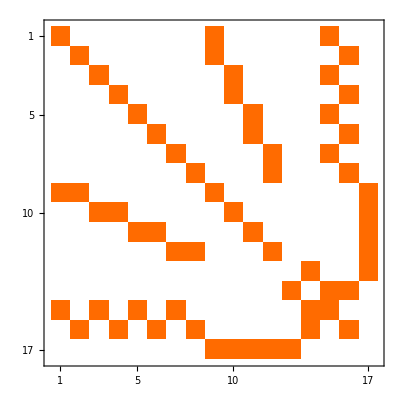
Adjacency matrix of orbit is: -Graphics-

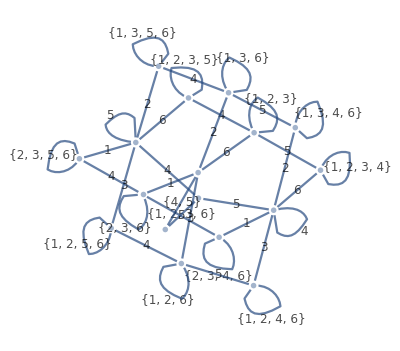

```mathematica
noqub=6;
myclass=2;

Print["First graph in orbit is: ",orbitsLigraphlist[[noqub]][[myclass]][[1]]]
Print["Number of graphs in Orbit is: ",Length@orbitsLigraphlist[[noqub]][[myclass]]]
Print["Adjacency matrix of orbit is: ",MatrixPlot@AdjacencyMatrix@orbitsLi[[noqub]][[myclass]]]

plotOrbitLi[noqub,myclass]
```

## Print labelled graph state orbitsLi adjacency matrices, ordered and grouped by graph state isomorphism

#### Plot Settings

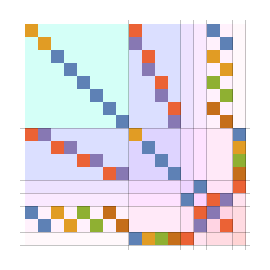
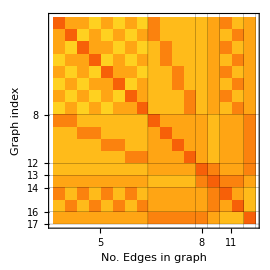
{-Graphics-,1 | RGBColor[0.368417, 0.506779, 0.709798]
2 | RGBColor[0.880722, 0.611041, 0.142051]
3 | RGBColor[0.560181, 0.691569, 0.194885]
4 | RGBColor[0.922526, 0.385626, 0.209179]
5 | RGBColor[0.528488, 0.470624, 0.701351]
6 | RGBColor[0.772079, 0.431554, 0.102387],-Graphics-,}

```mathematica
(*Adjust plot cosmetics*)
myframethickness=0.5;
myfontsize=10;
graphsize=270;

(*Adjust colour space for plots*)
satmod=0.17;
brightmod=1;

(*Difference in edge number required to be displayed on the plot*)
tickthresno=1;          (*in graph index*)
tickthresedge=1;     (*in edge number*)

plotOrbitMatrixLi[noqub,myclass]
```